```mathematica
(*Estoy usando k=3*)

Tnum={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16};
FidelDistil={0.996467185558,0.9963325115653,0.99616784244,0.9966054919885,0.995643490534751,0.9941715198371679,0.9951650105065329,0.994944958335576,0.995398568747117,0.9951175648472704,0.9941606529183525,0.9960089242842762,0.995260327777145,0.9952116552483329,0.9946678369732993,0.994124466054118};
FidelNodistil={0.99536478548,0.99500241982,0.99485044652092,0.99531987071452,0.9947321523151946,0.9939206401538478,0.994441317316312,0.994783498852324,0.9949987876306414,0.9951311065375892,0.994501490384656,0.9962842937460623,0.9956934221700977,0.995766260692126,0.9955050606821281,0.9948713766234288};
StdDistil={0.0043887044889,0.00442896167174,0.0060950214888,0.004556391809486,0.00452667094529160,0.00522405268896,0.004643702554527881,0.004833885508640751,0.004141503012533882,0.004269935370467163,0.0036230832461835553,0.0028825664134221273,0.0035183745684327643,0.00412193519433741,0.004187253413085307,0.004532410674393743};
StdNoDistil={0.00500625518922,0.004516578477855,0.0063254508798,0.004671581437273,0.00445808696308082,0.00484483399,0.003940744665245592,0.00426546146619410,0.003812475085358579,0.003978431048838828,0.0034001154144426373,0.0024244204489392014,0.0034978692880859954,0.003587977138096628,0.003898517386350445,0.004081709361170506};
```

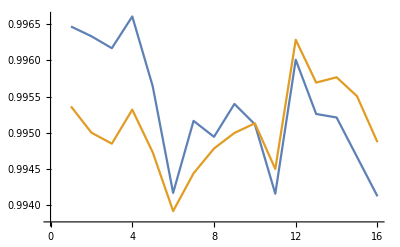

```mathematica
ListPlot[{FidelDistil,FidelNodistil},Joined->True]
```

```mathematica
Integrate[LegendreP[n,v,x],{x,0,1}]
```

∫_0^1 LegendreP[n,v,x]ⅆx

```mathematica
TraditionalForm[(((-1)^n+(-1)^m)/(Gamma[(n+3)/2] ((n-m)/2)!)) 2^(m-2) m Gamma[n/2] Gamma[(1/2) (n+m+1)]/;Element[n,Integers]&&n≥0&&Element[m,Integers]&&m≥0]
```

(2^(m-2) m ((-1)^m+(-1)^n) n/2 1/2 (m+n+1))/((n+3)/2 (n-m)/2!)/;n∈ℤ∧n≥0∧m∈ℤ∧m≥0